{alpha→1.0337×10^7,deltaH0→70.7844,deltaHlow→0.720563,beta→4.02364,Hz→27.4176}

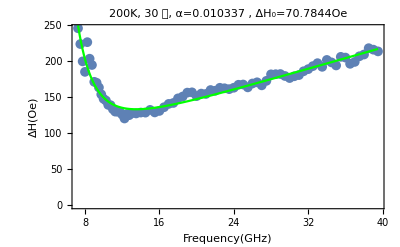

{{7.25,245.557},{7.5,223.642},{7.75,199.552},{8.,185.015},{8.25,226.23},{8.5,203.274},{8.75,194.534},{9.,171.187},{9.25,169.889},{9.5,163.317},{9.75,153.821},{10.,147.589},{10.25,145.26},{10.5,139.181},{10.75,138.789},{11.,133.252},{11.25,129.853},{11.5,129.796},{11.75,129.314},{12.,125.796},{12.25,120.318},{12.5,126.355},{12.75,124.917},{13.,127.46},{13.5,127.302},{14.,128.548},{14.5,128.45},{15.,132.24},{15.5,128.733},{16.,130.791},{16.5,135.927},{17.,140.544},{17.5,141.854},{18.,148.23},{18.5,150.759},{19.,156.208},{19.5,156.605},{20.,151.375},{20.5,154.835},{21.,154.35},{21.5,159.801},{22.,158.799},{22.5,162.921},{23.,162.231},{23.5,161.023},{24.,162.989},{24.5,167.109},{25.,167.476},{25.5,163.507},{26.,168.857},{26.5,170.527},{27.,166.306},{27.5,172.526},{28.,181.581},{28.5,181.779},{29.,182.005},{29.5,179.285},{30.,176.438},{30.5,178.914},{31.,180.542},{31.5,185.847},{32.,188.81},{32.5,192.993},{33.,197.085},{33.5,192.011},{34.,201.567},{34.5,198.16},{35.,193.928},{35.5,205.864},{36.,204.845},{36.5,196.194},{37.,198.825},{37.5,206.661},{38.,209.133},{38.5,217.879},{39.,215.833},{39.5,213.447}}

```mathematica
Clear["Global`*"];(*angle是与易轴[001]的夹角*)
h=6.626*10^-34;g=2;μ=9.27*10^-24;start`fre=5;stop`fre=40;T=200;angle=60;
T`points={300,250,200,150,100,75,50,40,30,25,20,15,10,8,4,2};angle`points={0,30,45,60,90,120,135};

fit`data={};
data=Import["C:\\Users\\aoubl\\Desktop\\Fit data\\CrO2 data\\["<>ToString[90-angle]<>" degree]-all data.xlsx","EmptyField"->"Empty"];
data=data[[1]];
data=Transpose@data;
T`position=3*First@FirstPosition[T`points,T]-2;
f`data=Drop[data[[T`position]],1];f`data=f`data/10^9;w`data=Drop[data[[T`position+2]],1];
positions=Position[w`data,"--"];w`data=Delete[w`data,positions];f`data=Delete[f`data,positions];

f`data=Select[f`data,#≠"Empty"&];w`data=Select[w`data,#≠"Empty"&];

f`new`data=Select[f`data,stop`fre>=#≥start`fre&];
lin`num=First@Flatten@Position[f`data,f`new`data[[1]]];

w`new`data=Take[w`data,{lin`num,Length@w`data}];

data=Table[{f`new`data[[i]],w`new`data[[i]]},{i,Length@f`new`data}];
deltaH1[f_,alpha_,deltaH0_,deltaHlow_,beta_,Hz_]:=deltaH0+alpha*h/(g*μ*10^-4)f+deltaHlow*(Hz/f)^beta;
deltaH2[f_,alpha_,deltaH0_,deltaHlow_,beta_,Hz_]:=deltaH0+alpha*h/(g*μ*10^-4)f+0*deltaHlow*(Hz/f)^beta;
fit`fun=deltaH1;
fit=FindFit[data,{fit`fun[f,alpha,deltaH0,deltaHlow,beta,Hz],{alpha>0.00*10^9,deltaH0>0,deltaHlow>0,beta>0,Hz>0}},{{alpha,0},{deltaH0,0},{deltaHlow,0},{beta,0},{Hz,1}}(*deltaH1[f,alpha,deltaH0],{{alpha,10^-3},{deltaH0,0}}*),f,MaxIterations->10000]
fig=Show[ListPlot[data,PlotMarkers->{Automatic,10}],Plot[Evaluate[fit`fun[f,alpha,deltaH0,deltaHlow,beta,Hz]/.fit],
	{f,Min@f`data,Max@f`data},PlotStyle->Green,PlotRange->All],Frame->True,
	FrameLabel->{"Frequency(GHz)","ΔH(Oe)"},PlotLabel->Text[Style[Framed[ToString[T]<>"K, "<>""<>ToString[90-angle]"度, "<>"α="<>ToString[10^-9*alpha/.fit]", "<>"ΔH_0="<>ToString[N[deltaH0/.fit,7]]<>"Oe"],
	Background->LightGreen,Bold]]]
data；
(*ex`data=Table[{f*10^9,fit`fun[f,alpha,deltaH0,deltaHlow,beta,Hz]/.fit},{f,8,45,0.05}];
Export["C:\\Users\\aoubl\\Desktop\\"<>ToString[90-angle]<>"degree,T="<>ToString[T]<>".xlsx",ex`data]
*)
```

```mathematica
(3.04+3.88+3.26+2.84+2.57+2.55+2.67+3.19+2.71)/9
```

2.96778

```mathematica
Mean[{3.04,3.88,3.26,2.84,2.57,2.55,2.67,3.19,2.71}]
```

2.96778

```mathematica
StandardDeviation[{3.04,3.88,3.26,2.84,2.57,2.55,2.67,3.19,2.71}]*Sqrt[Length[{3.04,3.88,3.26,2.84,2.57,2.55,2.67,3.19,2.71}]-1]/Sqrt[Length[{3.04,3.88,3.26,2.84,2.57,2.55,2.67,3.19,2.71}]]
```

0.405018

```mathematica
Mean[{4.82,5.86,5.47,4.62,5.20,5.03}]
```

5.16667

```mathematica
StandardDeviation[{4.82,5.86,5.47,4.62,5.20,5.03}]*Sqrt[Length[{4.82,5.86,5.47,4.62,5.20,5.03}]-1]/Sqrt[Length[{4.82,5.86,5.47,4.62,5.20,5.03}]]
```

0.410596

```mathematica
StandardDeviation[{0,1}]//N
```

0.707107

```mathematica
Variance[{0,1}]
```

1/2

m1

χ

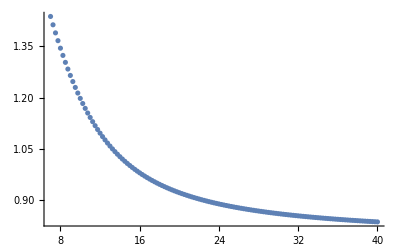

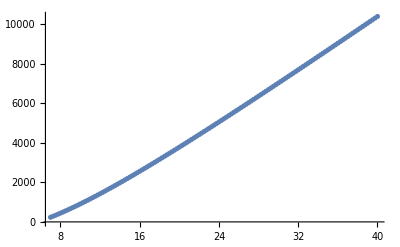

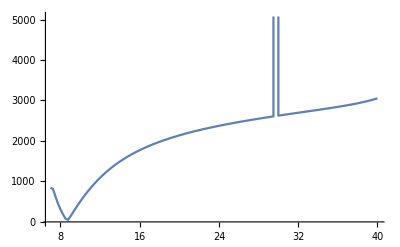

```mathematica
Clear["Global`*"];Clear[m1,m2];

K=7179.57;U=1067.66;B=8.01;g=2;μ=9.27*10^-24;ℏ=1.05*10^-34;
γ=10^-4*g*μ/ℏ;


m1[h_,phi`m_,phi`h_]:=h Cos[phi`m-phi`h]+K+B/4(3-Cos[4 phi`m])-U Sin[phi`m]^2;
m2[h_,phi`m_,phi`h_]:=h Cos[phi`m-phi`h]-B Cos[4 phi`m]-U Cos[2 phi`m];
χ[h_,f_,phi`m_,phi`h_,alpha_]:=(K*alpha *((2π f)/γ)(m1[h,phi`m,phi`h]^2+((2π f)/γ)^2))/((m1[h,phi`m,phi`h]*m2[h,phi`m,phi`h]-((2π f)/γ)^2)^2+alpha^2((2π f)/γ)^2(m1[h,phi`m,phi`h]+m2[h,phi`m,phi`h])^2);
(*χ[h_,h`r_,phi`m_,phi`h_,alpha_]:=(K*alpha *√(m1[h`r,phi`m,phi`h]*m2[h`r,phi`m,phi`h])(m1[h,phi`m,phi`h]^2+m1[h`r,phi`m,phi`h]*m2[h`r,phi`m,phi`h]))/((m1[h,phi`m,phi`h]*m2[h,phi`m,phi`h]-m1[h`r,phi`m,phi`h]*m2[h`r,phi`m,phi`h])^2+alpha^2(m1[h`r,phi`m,phi`h]*m2[h`r,phi`m,phi`h])(m1[h,phi`m,phi`h]+m2[h,phi`m,phi`h])^2);*)
(*χ[h_,f_,phi`m_,phi`h_,alpha_]:=(K*alpha *((2π f)/γ)^2*(m1[h,phi`m,phi`h]+m2[h,phi`m,phi`h]))/((m1[h,phi`m,phi`h]*m2[h,phi`m,phi`h]-((2π f)/γ)^2)^2+alpha^2((2π f)/γ)^2(m1[h,phi`m,phi`h]+m2[h,phi`m,phi`h])^2)*)
(*当phi`h=π/4时，phi`m=0.9567*)


 phi`h=π/4;alpha=0.0063; delta`h`data={};
ListPlot@drag`fre`data

f`data=Table[drag`fre`data[[i]][[1]],{i,Length@drag`fre`data}];
phi`m`data=Table[drag`fre`data[[i]][[2]],{i,Length@drag`fre`data}];
h`r`data=Table[Last@fre`field`data[[i]],{i,Length@fre`field`data}];
ListPlot[Table[{f`data[[i]],h`r`data[[i]]},{i,Length@f`data}]]

h`data=Table[i,{i,0,13000,10}];

χ`data[f_,phi`m_,phi`h_]:=Table[χ[h,f*10^9,phi`m,phi`h,alpha],{h,h`data}];
Do[data=χ`data[f`data[[j]],phi`m`data[[j]],phi`h];
fit`data=Table[{h`data[[i]],data[[i]]},{i,Length@h`data}];

fit=FindFit[fit`data,{(2A)/π*y/(4(h-h`r`data[[j]])^2+y^2),{A>0,y>0}},{A,y},h];


delta`h=y/.fit;
AppendTo[delta`h`data,{f`data[[j]],delta`h}],{j,Length@f`data}]
ListLinePlot@delta`h`data
```

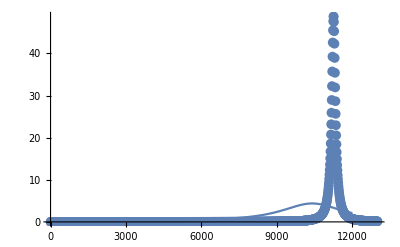

```mathematica
Show[ListPlot[fit`data,PlotMarkers->{Automatic,10},PlotRange->All],Plot[Evaluate[(2A)/π*y/(4(h-h`r`data[[-1]])^2+y^2)/.fit],{h,0,12000},PlotRange->All]]
```

{A→18517.9,y→186.824,c→6150.91}

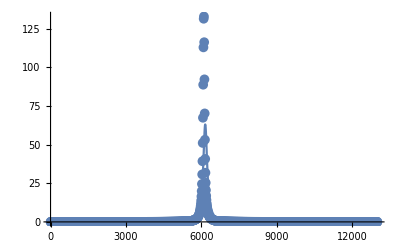

```mathematica
Clear["Global`*"]
q=First@Flatten@Position[drag`fre`data,25.];
Lor[A_,y_,c_]:=(2A)/π*y/(4(h-c)^2+y^2);
fit=FindFit[χ`h`data[[q]],{Lor[A,y,c],{A>0,y>0,c==h`r`data[[q]]}},{A,y,c},h,MaxIterations->Infinity]
Show[ListPlot[χ`h`data[[q]],PlotMarkers->{Automatic,10},PlotRange->All],Plot[Evaluate[(2A)/π*y/(4(h-c)^2+y^2)/.fit],{h,0,12000},PlotRange->All]]
```

```mathematica
f=Interpolation@linewidth`data
```

InterpolatingFunction[…]

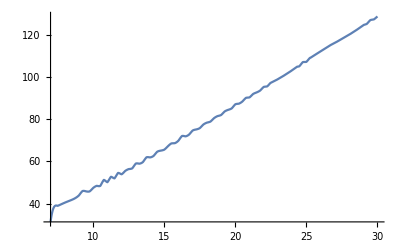

```mathematica
Plot[f[x],{x,7,30}]
```

```mathematica
delta`h`data
```

{2.55393,0.227297,0.182781,0.361578,0.171957,0.172421,0.16945,0.169822,0.167559,0.184163,0.166838,0.166478,0.16896,0.166833,0.166278,0.166938,0.16758,0.16618,0.166235,0.187522,0.166276,0.166074}

```mathematica
drag`data2
```

{{7,1.38429},{8,1.25517},{9,1.17337},{10,1.11396},{11,1.06839},{12,1.03274},{13,1.00451},{14,0.981158},{15,0.96177},{16,0.945821},{17,0.932087},{20,0.901621},{21,0.894071},{22,0.887274},{23,0.881169},{24,0.875721},{25,0.870931},{26,0.866736},{27,0.862594},{28,0.858955},{29,0.855794},{30,0.852686}}

```mathematica
f`data=Table[drag`data2[[i]][[1]],{i,Length@drag`data2}]
```

{7,8,9,10,11,12,13,14,15,16,17,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
2π*7*10^9/γ
```

2490.91